Plot of V(ξ)

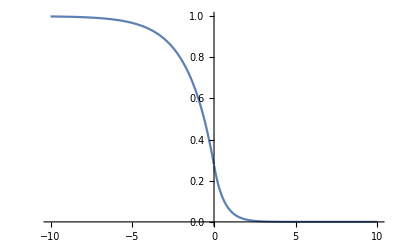

Plot of V(x,t)

-Graphics3D-

True

True

Plots of V'(ξ) and V'(x,t)

Piecewise[{{-(1/2 C (-C+√(4+C^2)) ⅇ^(1/2 (-C+√(4+C^2)) s)+1/2 √(4+C^2) (-C+√(4+C^2)) ⅇ^(1/2 (-C+√(4+C^2)) s))/(2 √(4+C^2)), s<0}, {((-C-√(4+C^2)) (-C+√(4+C^2)) ⅇ^(-1/2 (C+√(4+C^2)) s))/(4 √(4+C^2)), s>0}, {Indeterminate, True}}]

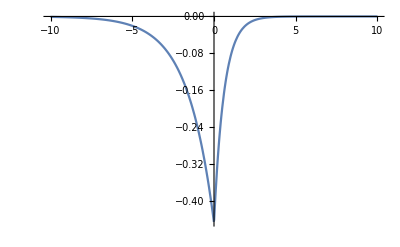

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

Perturbation eq: d_tψ - (d^2)_ξψ - c*d_ξψ + ψ = 0

1/2 (-1/2-C/(2 √(4+C^2))) (-C+√(4+C^2)) ⅇ^(1/2 (-C+√(4+C^2)) s)

1/2 (1/2-C/(2 √(4+C^2))) (-C-√(4+C^2)) ⅇ^(-1/2 (C+√(4+C^2)) s)

True

True

True

«1 more identical outputs»

```mathematica
(* Traveling wave solution: (x,t) -> ξ *)
Print["Plot of V(ξ)"]
V[s_, C_] = Piecewise[{
					{(-1/2-C/2/Sqrt[C^2+4])*Exp[s/2*(-C+Sqrt[C^2+4])]+1,s<0},
				  {(1/2-C/2/Sqrt[C^2+4])*Exp[-s/2*(C+Sqrt[C^2+4])],s>0}}];
Plot[V[s,1],{s,-10,10}]

(* Linear Stability Analysis with Perturbation
	Reference: LINEARIZING EQUATIONS ABOUT REST POINTS 
	"Formal method for linearizing a nonlinear ODE at a rest point ū"
 *)
Print["Plot of V(x,t)"]
v1[x_,t_, C_] = (-1/2-C/2/Sqrt[C^2+4])*Exp[(x-C*t)/2*(-C+Sqrt[C^2+4])]+1;
v2[x_,t_,C_] = (1/2-C/2/Sqrt[C^2+4])*Exp[-(x-C*t)/2*(C+Sqrt[C^2+4])];
Plot3D[Piecewise[{{v1[x,t,1],x<t},{v2[x,t,1],x>=t}}],{x,-10,10},{t,0,10}, ColorFunction->"AlpineColors", AxesLabel->Automatic]

(* 1. Show that Subscript[V, 1] and Subscript[V, 2] satisfy Subscript[d, t] V(x,t) - Subscript[d^2, x] V(x,t) + V(x,t) - H(V(x,t)-θ) 
		for their respective ranges*)
Simplify[D[v1[x,t,1],t]-D[D[v1[x,t,1],x],x]+v1[x,t,1]-1] == 0
Simplify[D[v2[x,t,1],t]-D[D[v2[x,t,1],x],x]+v2[x,t,1]] == 0

(* 2. Examine ψ(ξ,t) = V'(ξ) *)
Print["Plots of V'(ξ) and V'(x,t)"]
DV[s_,C_] = D[V[s,C],s]
Plot[DV[s,1],{s,-10,10}, PlotRange->All]

dv1[x_, t_, C_] = D[v1[x,t,C],x];
dv2[x_, t_,C_] = D[v2[x,t,C],x];
Plot3D[Piecewise[{{v1[x,t,1]+0*dv1[x,t,1], x<t},{v2[x,t,1]+0*dv2[x,t,1],x>t}}],{x,-10,10},{t,0,10}, PlotRange->All, ColorFunction->"AlpineColors", AxesLabel->Automatic]
Plot3D[Piecewise[{{v1[x,t,1]+0.99*dv1[x,t,1], x<t},{v2[x,t,1]+1*dv2[x,t,1],x>t}}],{x,-10,10},{t,0,10}, PlotRange->All, ColorFunction->"AlpineColors", AxesLabel->Automatic]
Plot3D[Piecewise[{{v1[x,t,1]+0.5*dv1[x,t,1], x<t},{v2[x,t,1]+0.5*dv2[x,t,1],x>t}}],{x,-10,10},{t,0,10}, PlotRange->All, ColorFunction->"AlpineColors", AxesLabel->Automatic]
Plot3D[Piecewise[{{v1[x,t,1]+0.01*dv1[x,t,1], x<t},{v2[x,t,1]+0.01*dv2[x,t,1],x>t}}],{x,-10,10},{t,0,10}, PlotRange->All, ColorFunction->"AlpineColors", AxesLabel->Automatic]

(* Check that Subscript[V, 1]'(ζ) and Subscript[V, 2]'(ξ) both satisfy perturbation equation for their ranges*)
Print["Perturbation eq: d_tψ - (d^2)_ξψ - c*d_ξψ + ψ = 0"]
s1[s_,C_] = (-1/2-C/2/Sqrt[C^2+4])*Exp[s/2*(-C+Sqrt[C^2+4])]+1;
s2[s_,C_] = (1/2-C/2/Sqrt[C^2+4])*Exp[-s/2*(C+Sqrt[C^2+4])];
ds1[s_,C_] = D[s1[s,C],s]
ds2[s_,C_] = D[s2[s,C],s]

Simplify[D[ds1[s,C],t]-D[D[ds1[s,C],s],s]-C*D[ds1[s,C],s]+ds1[s,C]] == 0
Simplify[D[ds2[s,C],t]-D[D[ds2[s,C],s],s]-C*D[ds2[s,C],s]+ds2[s,C]] == 0

(* check that it satisfies original *)

Simplify[D[D[ds1[s,C],s],s]+C*D[ds1[s,C],s]-ds1[s,C]] == 0
Simplify[D[D[ds2[s,C],s],s]+C*D[ds2[s,C],s]-ds2[s,C]] == 0
```

```mathematica
dS1[s_,C_] = Simplify[D[s1[s,C],s]];
dS2[s_,C_] = Simplify[D[s2[s,C],s]];
ddS1[s_,C_] = Simplify[D[dS1[s,C],s]];
ddS2[s_,C_] = Simplify[D[dS2[s,C],s]];

P1[s_,C_,l_] = -1/Sqrt[4+C^2*(l^2+1)]*Exp[1/2*(-c+Sqrt[4+C^2*(l^2+1)])]
P2[s_,C_,l_] = -1/Sqrt[4+C^2*(l^2+1)]*Exp[-1/2*(c+Sqrt[4+C^2*(l^2+1)])]
dP1[s_,C_,l_] = Simplify[D[P1[s,C,l],s]]
dP2[s_,C_,l_] = Simplify[D[P2[s,C,l],s]]
```

-(ⅇ^(1/2 (-c+√(4+C^2 (1+l^2)))))/(√(4+C^2 (1+l^2)))

-(ⅇ^(1/2 (-c-√(4+C^2 (1+l^2)))))/(√(4+C^2 (1+l^2)))